```mathematica
sfk=Import["G:\\calc-online\\gpd\\pic\\old\\pic3Dlist-k-n.wdx"];
sfl=Import["G:\\calc-online\\gpd\\pic\\old\\pic3Dlist-l-n.wdx"];
ft1=Query[1,1]@sfk;

gt1=Query[1,2]@sfl;

fp1=Interpolation[Flatten[ft1,1]];

gp1=Interpolation[Flatten[gt1,1]];
```

```mathematica
rfp1[x_,t_]=0.5*0.018546187157988524*x*fp1[x,t];

rgp1[x_,t_]=0.5*0.2522281453486439*x*gp1[x,t];
```

```mathematica
pf=Plot3D[rfp1[x,t],{x,-0.1,0.1},{t,-1,0},AxesLabel->{"y","t","yf_(π^+)^(bub)(y)"},LabelStyle->Directive[Thick,Black,12],PlotRange->All]
```

-Graphics3D-

```mathematica
pg=Plot3D[rgp1[x,t],{x,-0.1,0.1},{t,-1,0},AxesLabel->{"y","t","yg_(π^+)^(bub)(y)"},LabelStyle->Directive[Thick,Black,12],PlotRange->All]
```

-Graphics3D-

```mathematica
pathf=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"f-k-0.1.pdf"}];
pathg=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"g-l-0.1.pdf"}];
```

```mathematica
Export[pathf,pf]
Export[pathg,pg]
```

G:\calc-online\gpd\3dre\f-k-0.1.pdf

G:\calc-online\gpd\3dre\g-l-0.1.pdf

```mathematica
rfp11[x_,t_]=0.5*0.018546187157988524*x*fp1[x,-t];

rgp11[x_,t_]=0.5*0.2522281453486439*x*gp1[x,-t];
```

```mathematica
pf1=Plot3D[rfp11[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1},AxesLabel->{"y","-t(GeV^2)","yf_(π^+)^(bub)(y)"},LabelStyle->Directive[Thick,Black,12],PlotRange->All]
pg1=Plot3D[rgp11[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1},AxesLabel->{"y","-t(GeV^2)","yg_(π^+)^(bub)(y)"},LabelStyle->Directive[Thick,Black,12],PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
pathf1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"f-k-fan.pdf"}];
pathg1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"g-l-fan.pdf"}];
```

```mathematica
Export[pathf1,pf1]
Export[pathg1,pg1]
```

G:\calc-online\gpd\3dre\f-k-fan.pdf

G:\calc-online\gpd\3dre\g-l-fan.pdf

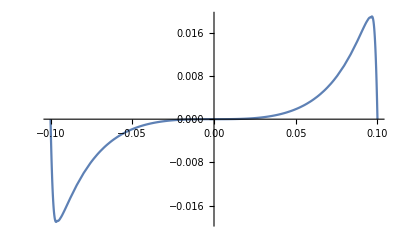

```mathematica
Plot[rfp1[x,-1],{x,-0.1,0.1}]
```

```mathematica
rfp1[0.0966,-1]
```

0.0190111+0. ⅈ

```mathematica
SubsuperscriptBox[yf,"π^+","(bub)"]//DisplayForm
```

yf_(π^+)^(bub)

```mathematica
SubsuperscriptBox[y g',"π^+","(bub)"]//DisplayForm
```

(y g')_(π^+)^(bub)

```mathematica
fn=Show[Plot3D[rfp11[x,t],{x,-0.1,0.1},{t,0.037,1}],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.52,-0.15,0}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],60Degree],Scaled[{-0.32,1,0.65}]]],
Graphics3D[Text[Style["y f_(π^+)^(bub)",Black,35,FontFamily->Times],Scaled[{-0.12,-0.2,0.8}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,1},{-1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{0,-2,0.8}]
gn=Show[Plot3D[rgp11[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.52,-0.15,0}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],60Degree],Scaled[{-0.32,1,0.65}]]],
Graphics3D[Text[Style["(y g')_(π^+)^(bub)",Black,35,FontFamily->Times],Scaled[{-0.08,-0.2,0.8}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,1},{-1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{0,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

```mathematica
pathfn=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\24414\\new",
"fn-kl-front.pdf"}];
pathgn=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\24414\\new",
"gn-kl-front.pdf"}];
```

```mathematica
Export[pathfn,fn]
Export[pathgn,gn]
```

G:\calc-online\gpd\3dre\24414\new\fn-kl-front.pdf

G:\calc-online\gpd\3dre\24414\new\gn-kl-front.pdf

```mathematica
gn2=Show[Plot3D[rgp11[x,t],{x,-0.1,0.1},{t,0.037,1},Lighting->{{"Directional",Orange,{{1,1,-3},{1,1,0}}},{"Directional",Orange,{{1,1,3},{1,1,0}}},{"Directional",Orange,{{1,1,0},{5,1,0}}},{"Directional",Orange,{{1,1,0},{-5,1,0}}}},PlotRange->All],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.52,-0.15,0}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],60Degree],Scaled[{-0.32,1,0.65}]]],
Graphics3D[Text[Style["(y g')_(π^+)^(bub)",Black,35,FontFamily->Times],Scaled[{1.12,-0.2,0.8}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{0,-2,0.8}]
```

-Graphics3D-

```mathematica
pathgn2=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\24414\\418t",
"gn-kl-front-2.pdf"}];
Export[pathgn2,gn2]
```

G:\calc-online\gpd\3dre\24414\418t\gn-kl-front-2.pdf

```mathematica
fn=Show[Plot3D[rfp11[x,t],{x,-0.1,0.1},{t,0.037,1}],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.48,-0.16,0}]]],Graphics3D[Text[Style["-t ",Black,30,FontFamily->Times],Scaled[{-0.16,-0.2,0.8}]]],Graphics3D[Text[Style["(GeV^2)",Black,30,FontFamily->Times],Scaled[{-0.18,-0.3,0.8}]]],
Graphics3D[Text[Style["yf_(π^+)^(bub)",Black,30,FontFamily->Times],Scaled[{1.62,0.3,0.2}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
gn=Show[Plot3D[rgp11[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.48,-0.16,0}]]],Graphics3D[Text[Style["-t ",Black,30,FontFamily->Times],Scaled[{-0.16,-0.2,0.8}]]],Graphics3D[Text[Style["(GeV^2)",Black,30,FontFamily->Times],Scaled[{-0.18,-0.3,0.8}]]],
Graphics3D[Text[Style["yg_(π^+)^(bub)",Black,30,FontFamily->Times],Scaled[{1.55,0.3,0.2}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

```mathematica
pathfn=FileNameJoin[{"G:\\output\\summary\\gpd\\24-4-7-mesonpic",
"fn-kl-left.pdf"}];
pathgn=FileNameJoin[{"G:\\output\\summary\\gpd\\24-4-7-mesonpic",
"gn-kl-left.pdf"}];
```

```mathematica
Export[pathfn,fn]
Export[pathgn,gn]
```

G:\output\summary\gpd\24-4-7-mesonpic\fn-kl-left.pdf

G:\output\summary\gpd\24-4-7-mesonpic\gn-kl-left.pdf

```mathematica
fn=Show[Plot3D[rfp11[x,t],{x,-0.1,0.1},{t,0.037,1},Lighting->{{"Directional",Orange,{{1,1,-3},{1,1,0}}},{"Directional",Orange,{{1,1,3},{1,1,0}}},{"Directional",Orange,{{1,1,0},{5,1,0}}},{"Directional",Orange,{{1,1,0},{-5,1,0}}}}],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.5,-0.15,0}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],60Degree],Scaled[{-0.32,1,0.65}]]],
Graphics3D[Text[Style["y f_(π^+)^(bub)",Black,35,FontFamily->Times],Scaled[{-0.13,-0.2,0.8}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,1},{-1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{0,-2,0.8}]
gn=Show[Plot3D[rgp11[x,t],{x,-0.1,0.1},{t,0.037,1},Lighting->{{"Directional",Orange,{{1,1,-3},{1,1,0}}},{"Directional",Orange,{{1,1,3},{1,1,0}}},{"Directional",Orange,{{1,1,0},{5,1,0}}},{"Directional",Orange,{{1,1,0},{-5,1,0}}}},PlotRange->All],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.5,-0.15,0}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],60Degree],Scaled[{-0.32,1,0.65}]]],
Graphics3D[Text[Style["(y g')_(π^+)^(bub)",Black,35,FontFamily->Times],Scaled[{-0.1,-0.2,0.8}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,1},{-1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{0,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

```mathematica
pathfn=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\24414\\418t",
"fn-kl-bright.pdf"}];
pathgn=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\24414\\418t",
"gn-kl-bright.pdf"}];
```

```mathematica
Export[pathfn,fn]
Export[pathgn,gn]
```

G:\calc-online\gpd\3dre\24414\418t\fn-kl-bright.pdf

G:\calc-online\gpd\3dre\24414\418t\gn-kl-bright.pdf